```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
aDist = StudentTDistribution[15,2,2.5];
data = RandomVariate[aDist,{10000}];
```

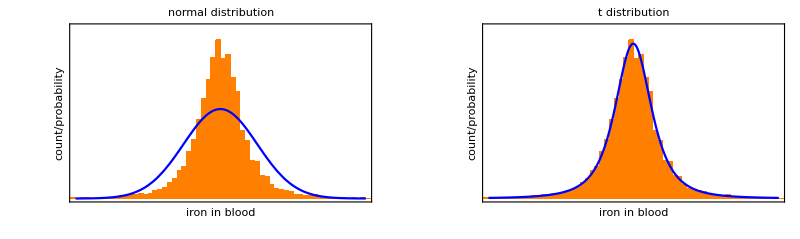

```mathematica
aUpper = 30;
aUpperY = 0.1;
aDeflationN = 0.5;
aDeflationT = 0.5;
{μ,σ}={FindDistributionParameters[data,NormalDistribution[a,b]][[1,2]],FindDistributionParameters[data,NormalDistribution[a,b]][[2,2]]};
g1=Show[Histogram[data,200,"Probability",PlotLabel->"normal distribution",PlotRange->{{0,aUpper},{0,aUpperY}},ChartStyle->Orange,Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"iron in blood","count/probability"},BaseStyle->{FontSize->16}],Plot[aDeflationN*PDF[NormalDistribution[μ,σ],x],{x,0,aUpper},PlotStyle->Blue]];
{μ,σ}={FindDistributionParameters[data,StudentTDistribution[a,b,2.5]][[1,2]],FindDistributionParameters[data,NormalDistribution[a,b]][[2,2]]};
g2=Show[Histogram[data,200,"Probability",PlotLabel->"t distribution",PlotRange->{{0,aUpper},{0,aUpperY}},ChartStyle->Orange,Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"iron in blood","count/probability"},BaseStyle->{FontSize->16}],Plot[aDeflationT*PDF[StudentTDistribution[μ,2,2.5],x],{x,0,aUpper},PlotStyle->Blue,PlotRange->{{0,aUpper},{0,aUpperY}}]];
gFinal=Show[GraphicsRow[{g1,g2}],ImageSize->800]
```

```mathematica
Export["Conjugate_lessonsNormT.pdf",gFinal]
```

Conjugate_lessonsNormT.pdf